```mathematica
SetDirectory[NotebookDirectory[]];
mat2 = Import["Displacements.txt","Table"];
```

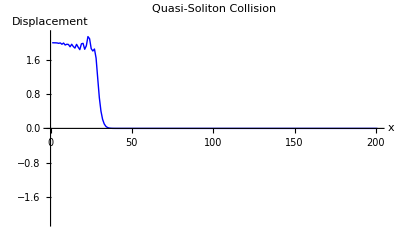

```mathematica
ListPlot[mat2[[All,100]],PlotRange-> {-2.2,2.2}, PlotStyle-> Blue,Joined->True,AxesLabel-> {x,Displacement},PlotLabel->"Quasi-Soliton Collision"]
```

## Exact Solution: Bistable spring system

The problem was reduced to

(c_o^2-v^2)/2(du/dz)^2=ψ[u].

Integrating,

```mathematica
∫(ⅆ u)/(√((1-u)^2+d^2)-lo)
```

(lo ArcTan[(-1+u)/(√(d^2-lo^2))])/(√(d^2-lo^2))+(lo ArcTan[(lo (-1+u))/(√(d^2-lo^2) √(d^2+(-1+u)^2))])/(√(d^2-lo^2))+Log[-1+√(d^2+(-1+u)^2)+u]

Converting the ArcTan terms to Log,

```mathematica
a[x_] := (-1+x)/(√(lo^2-d^2));
b[x_] := (lo (-1+x))/(√(lo^2-d^2) √(d^2+(-1+x)^2));
z[x_]:=√((co^2-v^2)/2)Log[(1-a[x])/(1+a[x])(1-b[x])/(1+b[x])(x-1+√((x-1)^2+d^2))^((2 √(lo^2-d^2))/lo)]
```

Parameters

```mathematica
lo=√2;
d=1;
co=√10;
v=2.812;
```

Inverse plot

Anti - Soliton Plot

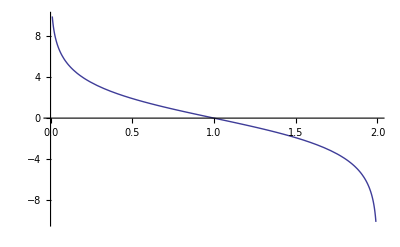

```mathematica
Plot[z[x],{x,0,2}]
```

Soliton Plot

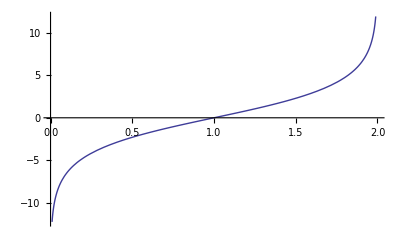

```mathematica
Plot[-z[x],{x,0,2}]
```

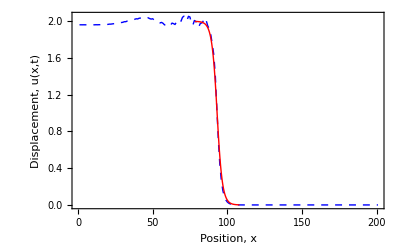

```mathematica
large =Show[ListPlot[mat2[[All,335]],Joined->True,AspectRatio->1/GoldenRatio, PlotStyle->Directive[Blue,Dashed],FrameLabel-> {"Position, x","Displacement, u(x,t)"},PlotLegends->Placed[LineLegend[{"Numerical Result"}],{Right,Top}],Frame->True],ParametricPlot[{z[x]+93.2,x},{x,0.001,1.999}, Frame->True,PlotStyle->Red,PlotLegends->Placed[{"Theoretical Result"},{Right,Top}]],BaseStyle->{FontFamily->"Times",14}]
```

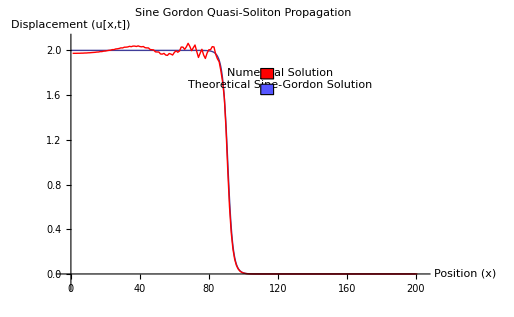

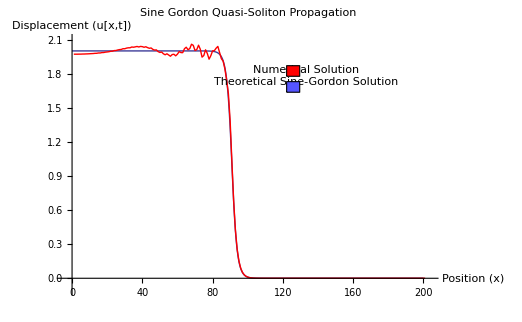

```mathematica
v=2.667/10;
```

```mathematica
A =ListContourPlot[Transpose[mat2],Axes-> True, FrameLabel-> {"Position(x)", "Time(t)"},PlotLabel-> "X-T contour plot of displacements",PlotLegends->Automatic]
```

```mathematica
B = Plot[x/v,{x,1,200},PlotStyle-> {Red,Thickness[0.008]}];
```

```mathematica
image=Show[A,B]
```

```mathematica
plots=Table[ListPlot[mat2[[All,2i]],Joined->True,PlotRange-> {-2.2,2.2}],{i,1,170}];
```

```mathematica
ListAnimate[plots]
```

```mathematica
Export["collision_animation.avi",plots]
```

collision_animation.avi

```mathematica
Export["largecontour.pdf",image]
```

largecontour.pdf

## Best Fit

```mathematica
mat = Import["slope.xlsx",{"Data",1}];
```

```mathematica
best = Table[0.2812i-0.1255,{i,1,600}];
```

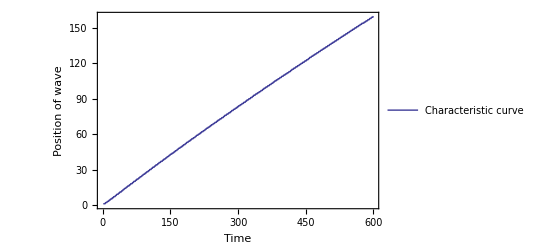

```mathematica
data = ListPlot[mat,Joined-> True,FrameLabel->{"Time","Position of wave"},PlotLegends->Placed[LineLegend[{"Characteristic  curve"}],{Right,Bottom}],Frame->
True,BaseStyle->{FontFamily->"Times",14}]
```

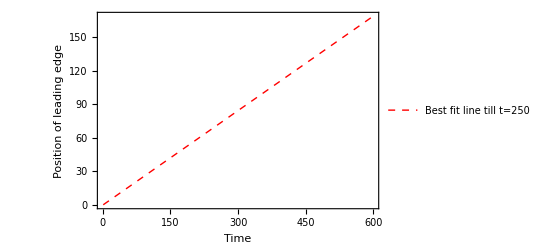

```mathematica
fit = ListPlot[best,Joined->True,FrameLabel->{"Time","Position of leading edge"},Frame->True,PlotLegends->Placed[LineLegend[{"Best fit line  till  t=250"}],{Right,Bottom}],PlotStyle->Directive[Red,Dashed],BaseStyle->{FontFamily->"Times",13.5}]
```

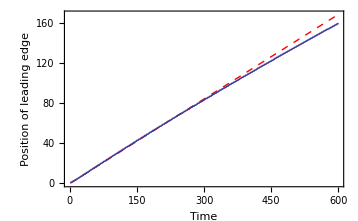

```mathematica
S = Show[fit,data]
```

```mathematica
Export["bestfit.pdf",S]
```

bestfit.pdf

```mathematica
mat3 = Table[mat2[[All,i]],{i,1,800}];
```

```mathematica
A = ListContourPlot[mat3, FrameLabel->{"Position, x","Time , t"},BaseStyle->{FontFamily->"Times",20},PlotLegends->BarLegend[Automatic, LabelStyle->{FontSize->20}]]
```

-Graphics-

```mathematica
best = Table[(i+0.1255)/0.2812,{i,1,200}];
```

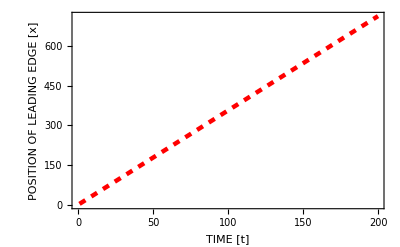

```mathematica
fit2 = ListPlot[best,Joined->True,FrameLabel->{"TIME [t]","POSITION OF LEADING EDGE [x]"},Frame->True,PlotStyle->{Dashed,Red,Thickness[0.008]}]
```

```mathematica
image2=Show[A,fit2]
```

-Graphics-

```mathematica
Export["largeContour.pdf",image2]
```

largeContour.pdf

Other Initial Sine-Gordon Comparisons

```mathematica
u[z_] := 4/π ArcTan[Exp[-√π w1/co z/(√(1-(v/co)^2))]]
```

```mathematica
u[z]
```

```mathematica
FullSimplify[co^2(D[u[z],z])^2]
```

(4 co^2 w1^2 Sech[(√π w1 z)/(co √(1-v^2/co^2))]^2)/(co^2 π-π v^2)

```mathematica
co
```

```mathematica
FullSimplify[Cos[π u[z]]]
```

Cos[4 ArcCot[ⅇ^((√π w1 z)/(co √(1-v^2/co^2)))]]

```mathematica
Integrate[(Sech[(√π w1 z)/(co √(1-v^2/co^2))])^2,{z,-∞, ∞}]
```

ConditionalExpression[(2 co √(1-v^2/co^2))/(√π w1),(Re[ⅈ^((co √(1-v^2/co^2))/(√π w1))]==0||Re[ⅈ^((co √(1-v^2/co^2))/(√π w1))]==1||Re[ⅈ^((co √(1-v^2/co^2))/(√π w1))]≥1||Re[ⅈ^((co √(1-v^2/co^2))/(√π w1))]≤0||ⅈ^((co √(1-v^2/co^2))/(√π w1))∉Reals)&&(Im[ⅈ^((co √(1-v^2/co^2))/(√π w1))]<0||Re[ⅈ^((co √(1-v^2/co^2))/(√π w1))]≥1||Im[ⅈ^((co √(1-v^2/co^2))/(√π w1))]>0||Re[ⅈ^((co √(1-v^2/co^2))/(√π w1))]≤0)&&Re[w1/(co √(1-v^2/co^2))]>0]

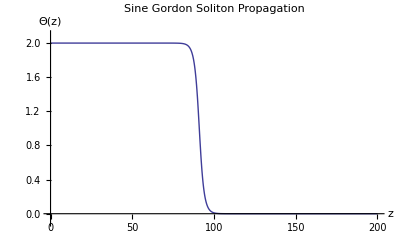

```mathematica
v = 2.662; (*Computed from the x-t diagram*)
co =√10; 
wo=(π*0.264911)^0.5; (*Max amplitude in Sine fit*)
u[z_] := 4/π ArcTan[Exp[-wo/co (z-91)/(√(1-(v/co)^2))]]
Plot[u[z],{z,0,200},PlotRange-> {-0.1,2.1}, PlotLabel->"Sine Gordon Soliton Propagation", AxesLabel-> {z,Θ[z]}]
```

```mathematica
u[z_] := 4/π ArcTan[Exp[-wo/co (z-91)/(√(1-(v/co)^2))]]
```

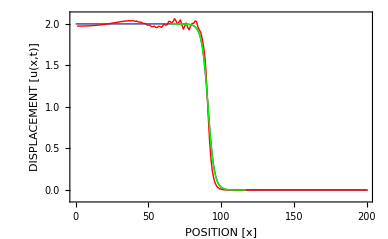

```mathematica
u[z_]:=2./(1.+ⅇ^(0.45454545454545453 (z-91)))
large =Show[Plot[u[z],{z,0,200},PlotRange-> {-0.1,2.1},  Frame->True,FrameLabel-> {"POSITION [x]","DISPLACEMENT [u(x,t)]"},PlotLegends->Placed[{"Theoretical Result"},{Right,Top}]],ListPlot[mat2[[All,326]],Joined->True, PlotStyle-> Red,AxesLabel-> {"Position (x)","Displacement (u(x,t))"},PlotLegends->Placed[{"Numerical Result"},{Right,Top}]],ParametricPlot[{z[x]+91,x},{x,0,2}, Frame->True,AspectRatio->2,PlotStyle->Green]]
```

```mathematica
Export["results_large.pdf",large]
```

results_large.pdf